Overdamped Brownian motion

```mathematica
$Assumptions={τ>0,τR>0,ω>0,τR Re[s]>-1,t>=0,τ-t>=0};
```

```mathematica
Psi[t_]=Exp[-Abs[t]/τR];
dPsi[t_]=-Sign[t]Exp[-Abs[t]/τR]/τR;
ddPsi1[t_]=Exp[-Abs[t]/τR]/τR^2;
ddPsi2[t_]=-2Exp[-Abs[t]/τR]DiracDelta[t]/τR;
```

```mathematica
lt1[s_]=Integrate[ddPsi1[t]Exp[-s t],{t,0,Infinity}]
lt2[s_]=Integrate[ddPsi2[t]Exp[-s t],{t,0,Infinity}]/.HeavisideTheta[0]->1/2
```

1/(τR (1+s τR))

-1/τR

```mathematica
f[s_]=-1/(s(lt1[s]+lt2[s]));

c0=SeriesCoefficient[f[s],{s,0,0}];

c1=SeriesCoefficient[f[s],{s,0,1}];

c2=SeriesCoefficient[f[s],{s,0,2}];
```

```mathematica
g[t_]=(t+τR)/(τ+2τR);
W0[τ_]=Psi[0]/2+1/2 Integrate[dPsi[τ-t]g[t],{t,0,τ}];
```

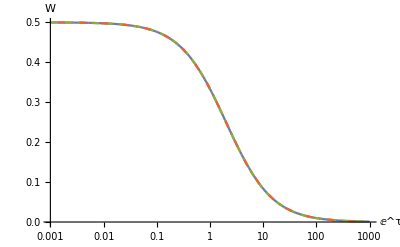

```mathematica
τR=1;
LogLinearPlot[{W0[τ]},{τ,0.001,1000}]
Clear[τR]
```

```mathematica
τR=1;

data=Table[{τ,ϵ1[τ]},{τ,0.001,0.01,0.001/100}];

Do[

aux=Table[{τ,ϵ1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi1.dat",data];

Clear[τR]
```